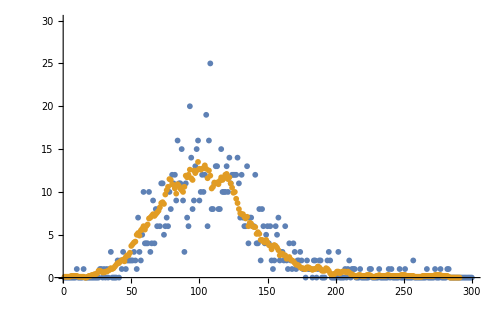

```mathematica
SetDirectory[NotebookDirectory[]];
data = Drop[Flatten[Import["energie_test.TKA", "table"]], 2];
data = data[[;;300]];

ListPlot[{data,data2}, PlotRange->{{0, 300},{0, 30}}, ImageSize->500]
```

```mathematica
Manipulate[
gaus = Table[PDF[NormalDistribution[0, σ], x], {x, -l, l, 1}];
data2=MovingAverage[data,ma];
dec = ListDeconvolve[gaus, data2,Method->{"DampedLS",a}];
ListPlot[{data2,dec},ImageSize->Large],{{σ,12},0.1,50,1},{{l,90},1,149,1},{{ma,1},1,20,1},{{a,15},1,20,1}]
```